-2.00035

NIntegrate::inumr: The integrand Log[1+√(1-4 Cos[t]^2 Sech[Times[«2»]]^2 Tanh[Times[«2»]]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in NumericalCalculus`Private`t$2205689 in the region {{0.,6.28319}}. NIntegrate obtained -5.5799+1.20563×10^-16 ⅈ and 0.0086598 for the integral and error estimates.

-1.77614+3.83765×10^-17 ⅈ

NIntegrate::inumr: The integrand Log[1+√(1-4 Cos[t]^2 Sech[Times[«2»]]^2 Tanh[Times[«2»]]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-10.2466

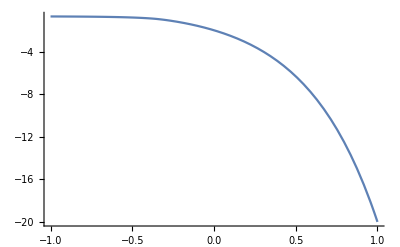

NIntegrate::inumr: The integrand Log[1+√(1-4 Cos[t]^2 Sech[Times[«2»]]^2 Tanh[Times[«2»]]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

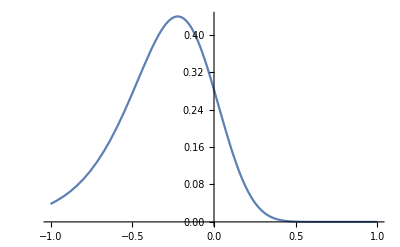

```mathematica
Needs["NumericalCalculus`"];
f[b_, j_]:=Module[{a = 2*b*j, k },
k = 2*Sinh[a]/Cosh[a]^2;
-Log[2]/2-Log[Cosh[a]] - NIntegrate[Log[1 + Sqrt[1 - (k*Cos[t])^2]],{t,0,Pi}]/  (2 * Pi)];
f1[b_, j_]:=(-Log[2]/2-Log[Cosh[2*b*j]] - NIntegrate[Log[1 + Sqrt[1 - (2*Sinh[2*b*j]/Cosh[2*b*j]^2*Cos[t])^2]],{t,0,Pi}]/  (2 * Pi));
c[b_, j_]:=-b^2 * (NumericalCalculus`ND[f[x,j],{x,2},b]);
c1[b_, j_]:=-b^2 * (NumericalCalculus`ND[f1[x,j],{x,2},b]);
NumericalCalculus`ND[f1[x,1],{x,2},0.44,Method->NIntegrate]
NumericalCalculus`ND[f1[x,1],{x,2},0.44,Method-> EulerSum]

Plot[f[10^b,1],{b,-1,1},PlotRange->All]
Plot[c[10^b,1],{b,-1,1},PlotRange->All]
Plot[c1[10^b,1],{b,-1,1},PlotRange->All]
```

```mathematica
Integrate[Log[1+Sqrt[1-p*Cos[t]^2]],{t,0,Pi},Assumptions->{p > -1, p < 1}]
```

Integrate[Log[1+√(1-p Cos[t]^2)],{t,0,π},Assumptions→{p>-1,p<1}]

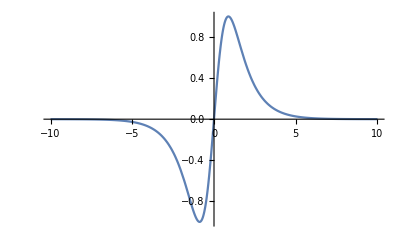

```mathematica
Plot[2*Sinh[x]/Cosh[x]^2,{x,-10,10},PlotRange->All]
```